```mathematica
ClearAll["Global`*"]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2025_fatscaling"}]
```

/Users/justinyeakel/Dropbox/PostDoc/2025_fatscaling

```mathematica
tt =α/(v*(ρ*μ)/β*α/n)
```

(n β)/(v μ ρ)

```mathematica
tt = 1/ρ*(n0*β0)/(μ*v0)*M^0.08/.(n0*β0)/(μ*v0)->tt0
```

(M^0.08 tt0)/ρ

```mathematica
tb = tb0*M^0.124
tc = tc0*M^0.196
```

M^0.124 tb0

M^0.196 tc0

```mathematica
ne = (tb*1/tc)/(tt*1/tc+tc*1/tc)
```

tb0/(M^0.072 tc0 (1.+tt0/(M^0.116 tc0 ρ)))

```mathematica
maxgut = ϵ*g0*M^0.897
```

g0 M^0.897 ϵ

```mathematica
costs = c0*M^-0.626
```

c0/M^0.626

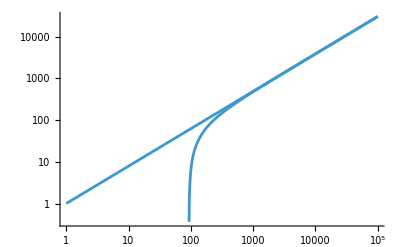

```mathematica
Show[
LogLogPlot[maxgut-costs/.{ϵ->1,g0->1,c0->1000},{M,1,10^5}],
LogLogPlot[maxgut/.{ϵ->1,g0->1,c0->1},{M,1,10^5}]
]
```

```mathematica
D[Log[2.6*M^0.147 - 1],Log[M]]
```

0

```mathematica
f[M_]:=2.6*M^0.147-1
D[Log[f[M]],M]*M
```

(0.3822 M^0.147)/(-1+2.6 M^0.147)

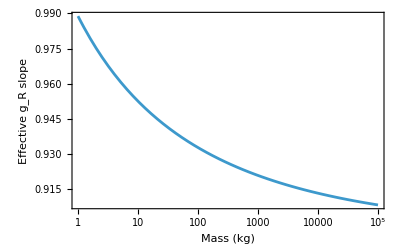

```mathematica
EffSlopePlot = LogLinearPlot[0.75 + (0.3822 M^0.14700000000000002)/(-1+2.6 M^0.147),{M,1,10^5},Frame->True,FrameLabel->{"Mass (kg)","Effective g_R slope"},LabelStyle->Directive[FontSize->16]]
```

```mathematica
Export[StringJoin[{namespace,"/figures/fig_gainsremainder_effslope.pdf"}],EffSlopePlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainsremainder_effslope.pdf

```mathematica
LogDerivative[f_,x_]:=FullSimplify[D[Log[f],x]*x]
```

```mathematica
dLogDeriv[f_,x_Symbol]:=Simplify[D[Log[f[x]],x]/D[Log[x],x]];
```

```mathematica
ld = LogDerivative[2.6*M^0.147 - 1,M]
```

0.147+1/(-6.80272+17.6871 M^0.147)

```mathematica
LogLinearPlot[0.75+ld,{M,1,10^5},Frame->True,FrameLabel->{"Mass (kg)","Effective g_R slope"},LabelStyle->Directive[FontSize->16]]
```

-Graphics-

Under POOR conditions

```mathematica
gREffectiveSlope = LogDerivative[g0*M^g1-c0*M^c1,M]
```

g1+(c0 (c1-g1) M^c1)/(c0 M^c1-g0 M^g1)

Using the parameterization for rho = 10^-7.5 (red) and rho = 10^-7.35 (orange) - corresponding to the dashed lines in the main gainsremainder plot

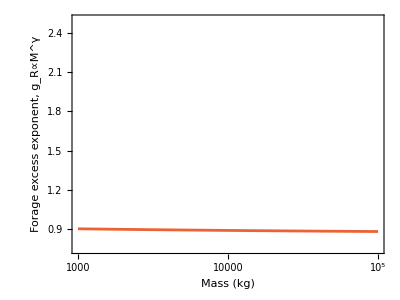

```mathematica
gREffectiveSlopePlotPoor = Show[
LogLinearPlot[gREffectiveSlope/.{c0->Exp[5.62],c1->0.75,g0->Exp[6.12],g1->0.86},{M,1000,10^5},PlotRange->{0.75,2.5},PlotStyle->ColorData[97,4],Frame->True,FrameLabel->{"Mass (kg)","Forage excess exponent, g_R∝M^γ"},LabelStyle->Directive[FontSize->16]]
(*,
LogLinearPlot[gREffectiveSlope/.{c0->Exp[5.92],c1->0.776,g0->Exp[5.04],g1->0.975},{M,1000,10^5},PlotStyle->ColorData[97,2]]}*)
,ImageSize->400,AspectRatio->0.75
]
```

```mathematica
gREffectiveSlope/.{c0->Exp[5.62],c1->0.75,g0->Exp[6.12],g1->0.86,M->10000}
```

0.891065

```mathematica
Export[StringJoin[{namespace,"/figures/fig_gainsremainder_effslope_lowrho.pdf"}],gREffectiveSlopePlotPoor]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainsremainder_effslope_lowrho.pdf

Travel Time derivation - with np = n/(w*h)

```mathematica
LogDerivative[f_,x_]:=FullSimplify[D[Log[f],x]*x]
```

```mathematica
ExpD= (α*β*(n/(w*h))^(ζ-1))/(μ*(α*(n/(w*h))^(ζ-2)-1))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1}
```

(M^β1 ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) α β0)/((-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ExpVolume= (α*β*(n/(w*h))^(ζ-1))/(μ*(α*(n/(w*h))^(ζ-2)-1))*w*h/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1}
```

(h0 M^(h1+w1+β1) ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) w0 α β0)/((-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ttravel = (α*β*(n/(w*h))^(ζ-1))/(v*μ*(α*(n/(w*h))^(ζ-2)-1))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
v->v0*M^v1,
w->w0*M^w1,
h->h0*M^h1}
```

(M^(-v1+β1) ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-1+ζ) α β0)/(v0 (-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) μ)

```mathematica
ttravelVAR=(1/v)^2*((α*(n/(w*h))^(ζ-2))^3)/((μ/(β*(n/(w*h))))^2*(α*(n/(w*h))^(ζ-2)-1)^2*(α*(n/(w*h))^(ζ-2)-2))/.{
β->β0*M^β1,
n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
v->v0*M^v1,
w->w0*M^w1,
h->h0*M^h1}
```

(M^(-2 h1-2 v1-2 w1+2 β1) (1+2 M^(n1+tb1+v1) n0 tb0 v0)^2 ((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-6+3 ζ) α^3 β0^2)/(h0^2 v0^2 w0^2 (-2+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α) (-1+((M^(-h1-w1) (1+2 M^(n1+tb1+v1) n0 tb0 v0))/(h0 w0))^(-2+ζ) α)^2 μ^2)

```mathematica
(*ttravel = 1/μ*(β0*M^β1*α*(n0*M^(n1)*(a0*M^(a1)))^(ζ-1))/(v0*M^v1*w0*M^w1*h0*M^h1*(α*(n0*M^(n1)*(a0*M^(a1)))^(ζ-2)-1))/.{a0->2*v0*tb0,a1->v1+tb1}*)
```

```mathematica
(*ttravel = (β0*M^β1*α*(n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1)))^(ζ-1))/(v0*M^v1*w0*M^w1*h0*M^h1*(α*(n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1)))^(ζ-2)-1))*)
```

```mathematica
ttravelParam = FullSimplify[ttravel/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}]
```

(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)

```mathematica
ttravelVARParam = FullSimplify[ttravelVAR/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}]
```

(7.10164×10^-6 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.297333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ^2)

```mathematica
ExpDParam= ExpD/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}
```

(0.002 0.666223^(-1+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-1+ζ) M^0.969 α)/((-1+0.666223^(-2+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-2+ζ) α) μ)

```mathematica
ExpVolumeParam = ExpVolume/.{
β0->0.002,
β1->0.969,
v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124
(*,ζ->1*)
}
```

(0.003002 0.666223^(-1+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-1+ζ) M^1.65933 α)/((-1+0.666223^(-2+ζ) ((1+0.99299/M^0.522)/M^0.690333)^(-2+ζ) α) μ)

```mathematica
zetavec = {1,1.5,2,2.15}
```

{1,1.5,2,2.15}

```mathematica
CompetitiveLoad=n/(w*h)/.{n->(1+n0*M^(n1)*(2*(v0*M^v1)*(tb0*M^tb1))),
w->w0*M^w1,
h->h0*M^h1};
CompetitiveLoadParam = CompetitiveLoad/.{v0->0.5,
v1->0.13,
w0->10,
w1->1/3,
h0->0.1501,
h1->0.357,
n0->5.45*10^-5,
n1->-0.776,
tb0->18220,
tb1->0.124};
```

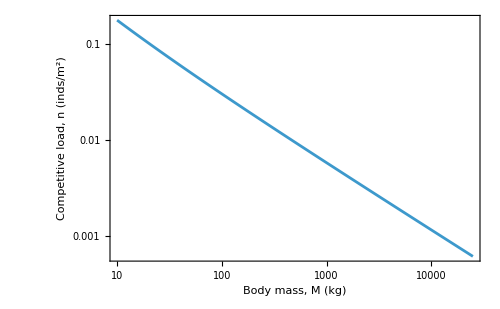

```mathematica
CompPlot = LogLogPlot[CompetitiveLoadParam,{M,10,25000},Frame->True,FrameLabel->{"Body mass, M (kg)","Competitive load, n (inds/m^2)"},LabelStyle->Directive[FontSize->16],ImageSize->500]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_compload.pdf"],CompPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_compload.pdf

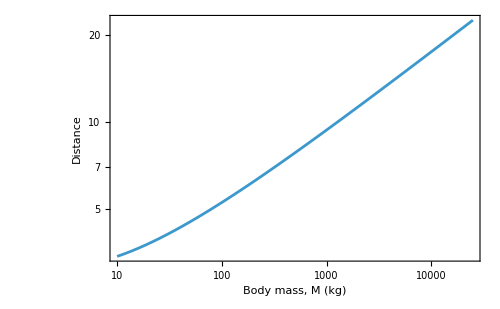

```mathematica
LogLogPlot[(α/(μ/β*(α/CompetitiveLoadParam-1))/.{μ->10^-3,α->4,q->1,β->β0*M^β1})/.{β0->0.002,β1->0.969},{M,10,25000},Frame->True,FrameLabel->{"Body mass, M (kg)","Distance"},LabelStyle->Directive[FontSize->16],ImageSize->500]
```

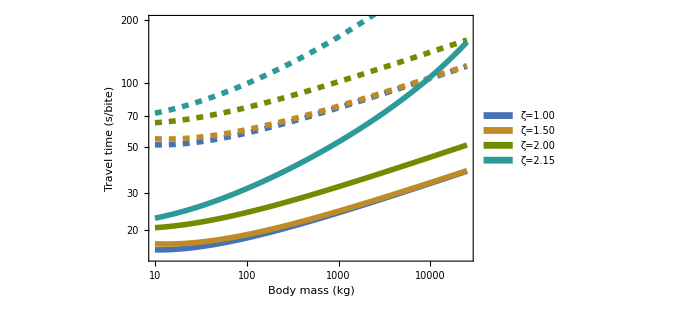

```mathematica
CD = 86;
PlotTravel = Show[
Flatten[{
LogLogPlot[ttravelParam/.{μ->10^-4,α->4,ζ->zetavec[[1]]},{M,10,25000},PlotRange->{15,200},PlotStyle->Directive[Thickness[0.008],Dashed,ColorData[CD,1]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16],PlotLegends->SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3],ColorData[CD,4]},{"ζ=1.00","ζ=1.50","ζ=2.00","ζ=2.15"}]],
Table[
LogLogPlot[ttravelParam/.{μ->10^-4,α->4,ζ->zetavec[[i]]},{M,10,25000},PlotStyle->Directive[Thickness[0.008],Dashed,ColorData[CD,i]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16]]
,{i,2,Length[zetavec]}],
Table[
LogLogPlot[ttravelParam/.{μ->10^-3.5,α->4,ζ->zetavec[[i]]},{M,10,25000},PlotStyle->Directive[Thickness[0.008],ColorData[CD,i]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16]]
,{i,1,Length[zetavec]}]
},1]
,ImageSize->500
]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_traveltime.pdf"],PlotTravel]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_traveltime.pdf

```mathematica
Table[ColorData[86,i],{i,5}]
```

{Hue[0.6, 0.6, 0.7],Hue[0.11, 0.8, 0.75],Hue[0.2, 1, 0.55],Hue[0.5, 0.7, 0.6],Hue[0.7, 0.55, 0.9]}

```mathematica
(*1) Define a robust converter that handles any ColorData output*)
colorToHex[color_]:=Module[
{rgb},(*force an RGB representation*)
rgb=List@@ColorConvert[color,"RGB"];
"#"<>StringJoin[IntegerString[Round[255 #],16,2]&/@rgb]];

(*2) Pull out the first three swatches from palette 86*)
Table[colorToHex[ColorData[86][i]],{i,1,5}]
```

{#4772b2,#bf8b26,#708c00,#2e9999,#8167e6}

```mathematica
Table[ColorData[i,j],{i,1,100},{j,1,5}]
```

{{RGBColor[0.24720000000000017, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.35317267440181815, 0.6]},{RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.26666666666666666, 0.],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882],RGBColor[1., 0.8784313725490196, 0.5058823529411764]},{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]},{RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451]},{RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353],RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785],RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197],RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434],RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706]},{RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353],RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784],RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569],RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353],RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862]},{RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745],RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745],RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197],RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509],RGBColor[0.28627450980392155, 0.23921568627450981, 0.2]},{RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354],RGBColor[1., 0.8549019607843137, 0.8274509803921568],RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647],RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059],RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393]},{RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608],RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784],RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627],RGBColor[0.9686274509803922, 0.6039215686274509, 0.],RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549]},{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765]},{RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235],RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098],RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628],RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902],RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451]},{RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294]},{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157]},{RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275],RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235],RGBColor[1., 0.35294117647058826, 0.12156862745098039],RGBColor[0.9725490196078431, 0.8, 0.5450980392156862],RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019]},{RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784],RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745],RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118]},{RGBColor[0.35294117647058826, 0.043137254901960784, 0.],RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549],RGBColor[0.42745098039215684, 0.2, 0.054901960784313725],RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235],RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392]},{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]},{RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098],RGBColor[0.6, 0.16470588235294117, 0.07450980392156863],RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098],RGBColor[0.796078431372549, 0.4, 0.09019607843137255],RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805]},{RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157],RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393],RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744],RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078],RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667]},{RGBColor[0.6549019607843137, 0.10980392156862745, 0.],RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373],RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549],RGBColor[0.996078431372549, 1., 0.8588235294117647],RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922]},{RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865],RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963],RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902],RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313],RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745]},{RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706],RGBColor[0.7372549019607844, 0.37254901960784315, 0.2],RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253],RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825],RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413]},{RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117],RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137],RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843],RGBColor[0.6431372549019608, 0.5215686274509804, 0.2],RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196]},{RGBColor[0.8705882352941177, 0.30980392156862746, 0.1450980392156863],RGBColor[0.9803921568627451, 0.37254901960784315, 0.19215686274509805],RGBColor[0.4196078431372549, 0.21176470588235294, 0.1411764705882353],RGBColor[0.8980392156862745, 0.611764705882353, 0.45098039215686275],RGBColor[0.7725490196078432, 0.5098039215686274, 0.15294117647058825]},{RGBColor[0.4, 0.10196078431372549, 0.],RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333],RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178],RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724],RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941]},{RGBColor[0.5882352941176471, 0.3058823529411765, 0.20784313725490197],RGBColor[0.7411764705882353, 0.5294117647058824, 0.3843137254901961],RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098],RGBColor[0.8235294117647058, 0.7254901960784313, 0.39215686274509803],RGBColor[0.8823529411764706, 0.8196078431372549, 0.6039215686274509]},{RGBColor[0.4, 0.3254901960784314, 0.2901960784313726],RGBColor[0.6705882352941176, 0.6274509803921569, 0.49411764705882355],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[0.8705882352941177, 0.9490196078431372, 0.7176470588235294],RGBColor[0.6705882352941176, 0.7607843137254902, 0.615686274509804]},{RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4]},{RGBColor[0.8235294117647058, 0.7333333333333333, 0.6862745098039216],RGBColor[0.40784313725490196, 0.42745098039215684, 0.26666666666666666],RGBColor[0.615686274509804, 0.6862745098039216, 0.48627450980392156],RGBColor[0.33725490196078434, 0.43529411764705883, 0.39215686274509803],RGBColor[0.5254901960784314, 0.592156862745098, 0.6]},{RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],RGBColor[1., 0.5568627450980392, 0.3215686274509804],RGBColor[1., 0.807843137254902, 0.4627450980392157],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785]},{RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863],RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745],RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.8235294117647058, 0.8941176470588236, 0.9490196078431372]},{RGBColor[0.8705882352941177, 0.3411764705882353, 0.0196078431372549],RGBColor[0.8117647058823529, 0.3686274509803922, 0.06274509803921569],RGBColor[0.9372549019607843, 0.7176470588235294, 0.14901960784313725],RGBColor[0.13333333333333333, 0.2784313725490196, 0.10980392156862745],RGBColor[0.2549019607843137, 0.5411764705882353, 0.3215686274509804]},{RGBColor[0.7450980392156863, 0.30196078431372547, 0.],RGBColor[0.8823529411764706, 0.49411764705882355, 0.09411764705882353],RGBColor[0.8274509803921568, 0.8117647058823529, 0.4549019607843137],RGBColor[0.6823529411764706, 0.6901960784313725, 0.6470588235294118],RGBColor[0.611764705882353, 0.6901960784313725, 0.3411764705882353]},{RGBColor[0.7372549019607844, 0.4745098039215686, 0.2],RGBColor[0.5058823529411764, 0.28627450980392155, 0.047058823529411764],RGBColor[0.24705882352941178, 0.2980392156862745, 0.25882352941176473],RGBColor[0.396078431372549, 0.5450980392156862, 0.43137254901960786],RGBColor[0.5411764705882353, 0.5019607843137255, 0.6352941176470588]},{RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392],RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353],RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529],RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865],RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392]},{RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333]},{RGBColor[0.692302, 0.618341, 0.375174],RGBColor[0.4533, 0.506783, 0.175158],RGBColor[0.814481, 0.0706188, 0.0264134],RGBColor[0.705882, 0.578744, 0.240635],RGBColor[0.606332, 0.199557, 0.0732433]},{RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4]},{RGBColor[0.855879, 0.665019, 0.302953],RGBColor[0.780926, 0.753979, 0.604883],RGBColor[0.807065, 0.511589, 0.285222],RGBColor[0.866682, 0.764462, 0.397528],RGBColor[0.735576, 0.755901, 0.876387]},{GrayLevel[0.501961],GrayLevel[0.660639],RGBColor[0.593454, 0.888609, 0.918547],RGBColor[0.346227, 0.71075, 0.927596],RGBColor[0.355077, 0.714931, 0.54519]},{RGBColor[0.805432, 0.43006, 0.438804],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.63801, 0.0991073, 0.147646],RGBColor[0.733028, 0.239811, 0.279622],RGBColor[0.873304, 0.567529, 0.217945]},{RGBColor[0.823529, 0.788464, 0.657969],RGBColor[0.710414, 0.677302, 0.556176],RGBColor[0.687785, 0.640955, 0.477546],RGBColor[0.610864, 0.569268, 0.42414],RGBColor[0.493217, 0.434531, 0.340993]},{RGBColor[0.714931, 0.604425, 0.0751812],RGBColor[0.950225, 0.85272, 0.062623],RGBColor[0.968322, 0.939544, 0.0737011],RGBColor[0.987869, 1, 0.364248],RGBColor[0.904982, 0.80087, 0.0986343]},{RGBColor[1, 0.753262, 0.0437629],RGBColor[0.945708, 0.661402, 0.128328],RGBColor[1, 0.854948, 0.112474],RGBColor[0.850675, 0.561089, 0.0324254],RGBColor[1, 0.70927, 0.144472]},{RGBColor[0.773754, 0.420615, 0.187213],RGBColor[0.443442, 0.110262, 0.100633],RGBColor[0.877699, 0.728923, 0.228702],RGBColor[0.882353, 0.597772, 0.124285],RGBColor[0.266972, 0.112123, 0.117922]},{RGBColor[0.922972, 0.986419, 0.46389],RGBColor[0.501961, 0, 0],RGBColor[0.773754, 0.146609, 0.00296025],RGBColor[0.986419, 0.905287, 0.0534218],RGBColor[0.417227, 0.46154, 0.157656]},{RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.909499, 0.613916, 0.204196],RGBColor[0.806577, 0.385397, 0.762768],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.378897, 0.873304, 0.787549]},{RGBColor[0.709133, 0.747539, 0.83711],RGBColor[0.813855, 0.974746, 0.996429],RGBColor[0.76527, 0.954757, 0.912932],RGBColor[0.581781, 0.801038, 0.828061],RGBColor[0.66154, 0.87277, 0.882353]},{RGBColor[0.814481, 0.432822, 0.406287],RGBColor[1, 0.4, 0.4],RGBColor[0.954757, 0.215122, 0.0483253],RGBColor[0.268833, 0.246555, 0.506783],RGBColor[0.570138, 0.0971847, 0.0971847]},{RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463]},{RGBColor[0.742077, 0.0624857, 0.00605783],RGBColor[0, 0.501961, 0],RGBColor[0.891279, 0.721172, 0.777905],RGBColor[0.0620432, 0.521904, 0.704387],RGBColor[0.823529, 0.663981, 0.00828565]},{RGBColor[0.151827, 0.281636, 0.714931],RGBColor[0.753628, 0.82591, 0.991257],RGBColor[1, 0.937255, 0.224521],RGBColor[0.915969, 0.930159, 0.97409],RGBColor[1, 0.993332, 0.352972]},{RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904]},{RGBColor[0.70135, 0.093019, 0.00140383],RGBColor[0.289647, 0.222614, 0.484169],RGBColor[0.98677, 0.98793, 0.458686],RGBColor[0.42948, 0.524086, 0.719463],RGBColor[0.30808, 0.443137, 0.124895]},{RGBColor[0.90045, 0.765209, 0.745602],RGBColor[0.864256, 0.544503, 0.601099],RGBColor[0.719463, 0.374975, 0.35935],RGBColor[0.312215, 0.134813, 0.182895],RGBColor[0.488685, 0.199069, 0.220294]},{RGBColor[0.73, 0.245061, 0.1971],RGBColor[0.1971, 0.5022473119339774, 0.73],RGBColor[0.5356156238679548, 0.73, 0.1971],RGBColor[0.5712760641980676, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.5379077522640902]},{Hue[0.5, 0.5, 0.4],Hue[0.11, 0.75, 0.8],Hue[0.04, 1, 0.8],Hue[0.5, 0.5, 0.6],Hue[0.67, 0.33, 0.5]},{Hue[0.64, 0.5, 0.7],Hue[0.11, 0.75, 0.7],Hue[0.5, 0.7, 0.6],Hue[0.2, 0.66, 0.66],Hue[0.7, 0.4, 0.8]},{Hue[0.61, 0.7, 1],Hue[0.17, 0.4, 0.65],Hue[0.64, 0.5, 0.75],Hue[0.45, 0.4, 0.7],Hue[0.55, 0.8, 0.6]},{Hue[0, 1, 1],Hue[0.1, 0.7, 0.9],Hue[0, 0.75, 0.8],Hue[0.05, 0.8, 1],Hue[0.05, 1, 0.8]},{Hue[0.55, 1, 0.7],Hue[0.06, 1, 0.9],Hue[0.25, 1, 0.55],Hue[0.11, 0.9, 0.85],Hue[0.5, 1, 0.5]},{Hue[0.12, 0.8, 0.8],Hue[0.17, 0.6, 0.5],Hue[0.1, 0.83, 0.96],Hue[0.1, 1, 0.7],Hue[0.11, 0.6, 0.8]},{Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75]},{Hue[0.94, 0.7, 0.9],Hue[0, 0.5, 1],Hue[0.9, 0.5, 0.7],Hue[0.05, 0.5, 0.85],Hue[0.9, 0.67, 0.85]},{Hue[0.08, 1, 0.88],Hue[0.11, 1, 0.66],Hue[0.17, 0.67, 0.66],Hue[0, 0.33, 0.66],Hue[0.11, 0.9, 0.85]},{Hue[0.12, 0.8, 0.8],Hue[0.17, 0.67, 0.48],Hue[0.11, 0.6, 0.7],Hue[0.06, 0.75, 0.76],Hue[0.17, 0.75, 0.64]},{Hue[0.33, 0.5, 0.6],Hue[0.11, 0.75, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.83, 0.33, 0.75],Hue[0.17, 0.5, 0.5]},{Hue[0.22, 1, 0.51],Hue[0.21, 0.8, 0.85],Hue[0.28, 0.75, 0.6],Hue[0.25, 1, 0.85],Hue[0.45, 1, 0.55]},{Hue[0, 1, 0.68],Hue[0.15, 1, 0.25],Hue[0.03, 1, 0.85],Hue[0, 1, 0.4],Hue[0.05, 0.9, 0.7]},{Hue[0.08, 1, 0.68],Hue[0.17, 0.5, 0.34],Hue[0.11, 0.75, 0.68],Hue[0.08, 0.67, 0.51],Hue[0.12, 0.8, 0.85]},{Hue[0.21, 1, 0.56],Hue[0.13, 0.83, 0.8],Hue[0.22, 1, 0.42],Hue[0.25, 0.8, 0.7],Hue[0.17, 0.67, 0.42]},{Hue[0.06, 1, 0.85],Hue[0.11, 0.9, 0.8],Hue[0, 0.5, 0.44],Hue[0.06, 0.8, 0.8],Hue[0.08, 1, 0.5]},{Hue[0.04, 1, 0.8],Hue[0.08, 0.8, 0.9],Hue[0.07, 1, 0.75],Hue[0.08, 1, 1],Hue[0.03, 0.8, 0.75]},{Hue[0.58, 1, 0.5],Hue[0.12, 1, 0.9],Hue[0, 1, 0.75],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7]},{Hue[0.6, 0.7, 0.8],Hue[0.22, 1, 0.7],Hue[0.75, 0.6, 0.7],Hue[0.5, 1, 0.65],Hue[0.7, 0.6, 0.7]},{Hue[0.08, 1, 1],Hue[0.17, 0.8, 0.5],Hue[0, 1, 0.8],Hue[0.06, 1, 0.8],Hue[0.33, 0.5, 0.5]},{Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72]},{Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72]},{Hue[0.6, 0.6, 0.7],Hue[0.11, 0.8, 0.75],Hue[0.2, 1, 0.55],Hue[0.5, 0.7, 0.6],Hue[0.7, 0.55, 0.9]},{Hue[0.05, 1, 1],Hue[0.1, 1, 0.95],Hue[0, 0.7, 0.9],Hue[0.15, 0.7, 0.85],Hue[0.83, 0.33, 0.75]},{Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1]},{Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6]},{Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9]},{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6]},{Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8]},{Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55]},{RGBColor[0.21014945601196963, 0.4780271451416804, 0.8021972051611045],RGBColor[0.7072977906722242, 0.3673486887042061, 0.2257297555221048],RGBColor[0., 0.5478586253818709, 0.48916968117936716],RGBColor[0.645200512498271, 0.3592874294783095, 0.6737365089505112],RGBColor[0.4795219159573389, 0.47945002873891307, 0.08945260272681405]},{RGBColor[0.5477240862612719, 0.6781403431438215, 0.9198750056398158],RGBColor[0.8706107786759318, 0.6048280298927478, 0.49228582375949304],RGBColor[0.31565582871733483, 0.7398377411666651, 0.6872937358891439],RGBColor[0.8116708417619926, 0.6012303372612685, 0.8258504778335548],RGBColor[0.6930195290945362, 0.6799726542041913, 0.4199367485764253]},{RGBColor[0.23780781740448295, 0.6887454706969063, 1.],RGBColor[1., 0.519599248047801, 0.30967746609094066],RGBColor[0., 0.7904116386138192, 0.7051174262187454],RGBColor[0.9363861336280549, 0.506536968871292, 0.981106505571294],RGBColor[0.6869591096151808, 0.6905739930724654, 0.057750228241946755]},{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514]},{RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797]},{RGBColor[0.0684356, 0.645252, 0.782123],RGBColor[0.98993, 0.699651, 0.0271887],RGBColor[0.450866, 0.379481, 1.],RGBColor[0.369422, 0.7, 0.229826],RGBColor[0.942659, 0.463296, 0.151884]}}

```mathematica
ttravelValues = Table[{10^i,ttravelParam/.{μ->10^-4,α->4,ζ->1,M->10^i}},{i,3,4,0.1}];
(*Assume neValues is defined as in your code*)
logttravelValues=Log10@ttravelValues;
(*Fit a linear model to the log-log data*)
ttfit=LinearModelFit[logttravelValues,x,x]
(*Extract the slope*)
slope=ttfit["BestFitParameters"][[2]]
```

FittedModel[…]

0.140254

```mathematica
(*ne = FullSimplify[(tb0*M^tb1)/(1/μ*tt0*M^tt1+(tc0*M^tc1)*(β0*M^β1))]*)
```

```mathematica
nefullParam = FullSimplify[(tb0*M^tb1)/(ttravelParam+(tc0*M^tc1)*(β0*M^β1))/.{
β0->0.002,
β1->0.969,
tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196
}]
```

(18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
nefullDeltaParam = (tb0*M^tb1)/(ttravelParam+(tc0*M^tc1)*(β0*M^β1))+ 1/2*(2*(tb0*M^tb1))/((ttravelParam+(tc0*M^tc1)*(β0*M^β1))^3)*ttravelVARParam/.{
β0->0.002,
β1->0.969,
tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196
}
```

(18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.129392 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.421333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^3 μ^2)

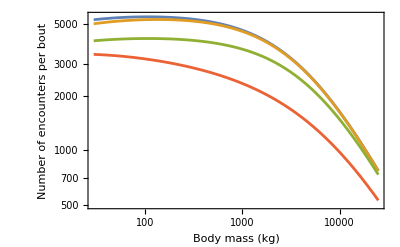

```mathematica
Show[
Table[
LogLogPlot[(nefullParam)/.{μ->10^-3,α->4,ζ->zetavec[[i]]},{M,30,25000},PlotRange->{500,5500},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Number of encounters per bout"}],
{i,1,Length[zetavec]}]
]
```

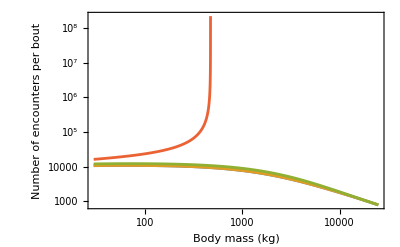

```mathematica
Show[
Table[
LogLogPlot[(nefullDeltaParam)/.{μ->10^-3,α->4,ζ->zetavec[[i]]},{M,30,25000},PlotRange->{500,All},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Number of encounters per bout"}],
{i,1,Length[zetavec]}]
]
```

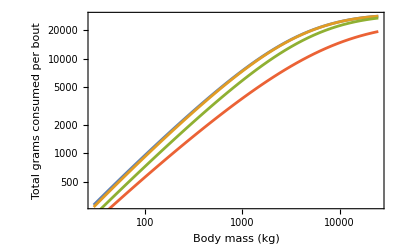

```mathematica
Show[
Table[
LogLogPlot[(nefullParam*(β0*M^β1))/.{β0->0.002,β1->0.969,μ->10^-3,α->4,ζ->zetavec[[i]]},{M,30,25000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Total grams consumed per bout"}],
{i,1,Length[zetavec]}]
]
```

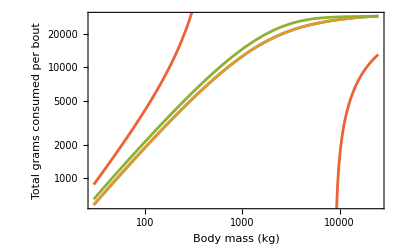

```mathematica
Show[
Table[
LogLogPlot[(nefullDeltaParam*(β0*M^β1))/.{β0->0.002,β1->0.969,μ->10^-3,α->4,ζ->zetavec[[i]]},{M,30,25000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Total grams consumed per bout"}],
{i,1,Length[zetavec]}]
]
```

```mathematica
nefullParam/.{μ->10^-4,α->3,M->10000}
```

57088.5/(24.3811+(272384. 0.00116357^(-1+ζ))/(-1+3 0.00116357^(-2+ζ)))

```mathematica
neValues = Table[{10^i,nefullParam/.{μ->10^-2,α->4,ζ->1,M->10^i}},{i,4,4.5,0.1}];
(*Assume neValues is defined as in your code*)
logNeValues=Log10@neValues;
(*Fit a linear model to the log-log data*)
fit=LinearModelFit[logNeValues,x,x]
(*Extract the slope*)
slope=fit["BestFitParameters"][[2]]
int = fit["BestFitParameters"][[1]]
```

FittedModel[…]

-1.01596

7.41591

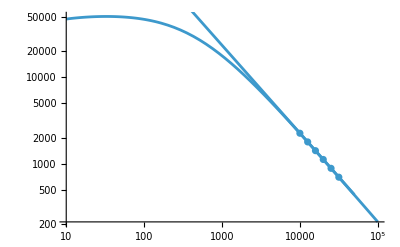

```mathematica
Show[
LogLogPlot[nefullParam/.{μ->10^-2,α->4,ζ->1},{M,10,10^5}],
ListLogLogPlot[neValues],
LogLogPlot[10^int*M^slope ,{M,10,50000}]
]
```

```mathematica
gainsParam = nefullParam*(β0*M^β1)*ϵ/.{β0->0.002,β1->0.969,ϵ->18.2}
```

(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
gainsDeltaParam = nefullDeltaParam*(β0*M^β1)*ϵ/.{β0->0.002,β1->0.969,ϵ->18.2}
```

0.0364 M^0.969 ((18220 M^0.124)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.129392 (1+0.99299/M^0.522)^2 ((0.661552+0.666223 M^0.522)/M^1.21233)^(3 (-2+ζ)) M^0.421333 α^3)/((-2+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^3 μ^2))

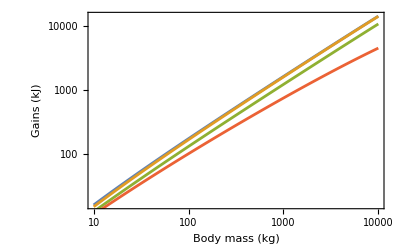

```mathematica
Show[
Table[
LogLogPlot[gainsParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Gains (kJ)"}],
{i,1,Length[zetavec]}]
]
```

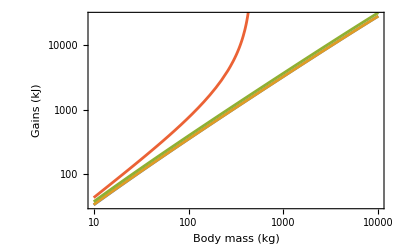

```mathematica
Show[
Table[
LogLogPlot[gainsDeltaParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Gains (kJ)"}],
{i,1,Length[zetavec]}]
]
```

```mathematica
costsParam = nefullParam*ttravelParam*(F0*M^F1) + nefullParam*(tc0*M^tc1)*(B0*M^B1) + tday*(B0*M^B1) - (tb0*M^tb1)*(B0*M^B1)/.{tb0->18220,
tb1->0.124,
tc0->0.2667,
tc1->0.196,
F0->0.0084,(*0.001 kJps * f0_g * (1000)^(0.75)*)
F1->0.75,
B0->0.0032,(*0.001 kJps * b0_g * (1000)^(0.75)*)
B1->0.75,
tday -> 24*60*60}
```

276.48 M^0.75-58.304 M^0.874+(15.5497 M^1.07)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))+(0.612192 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^1.713 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)) μ)

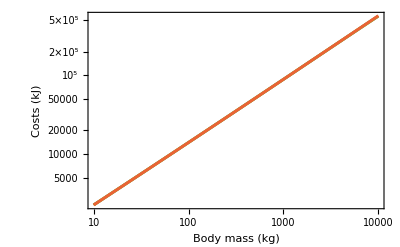

```mathematica
Show[
Table[
LogLogPlot[costsParam/.{α->4,μ->10^-5,ζ->zetavec[[i]]},{M,10,10000},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
{i,1,Length[zetavec]}]
]
```

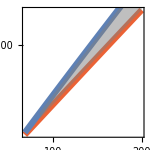

```mathematica
muExp = -3.06;
insetPlot = Show[
LogLogPlot[costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,80,200},PlotStyle->Directive[Thickness[0.03],ColorData[97,4]],Frame->True,FrameTicks->None,(*FrameLabel->{"Body mass (kg)","Gains,  Costs (kJ)"},*)LabelStyle->Directive[FontSize->16],FrameStyle->Directive[Black,Thick]],
LogLogPlot[gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,80,200},PlotStyle->Directive[Thickness[0.03],ColorData[97,1]],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
LogLogPlot[{costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]}},{M,90,200},PlotStyle->Transparent,Filling->{1->{{2},{Directive[Gray,Opacity[0.5]]}}}]
, AspectRatio->1,ImageSize->150
]
```

```mathematica
simgaincost = Import[StringJoin[namespace,"/herbforagingsim/data/simdata/gaincostpoor_data.csv"]][[2;;All]];
```

```mathematica
simgain = Transpose[{simgaincost[[All,1]],simgaincost[[All,2]]}];
simcost = Transpose[{simgaincost[[All,1]],simgaincost[[All,3]]}];
```

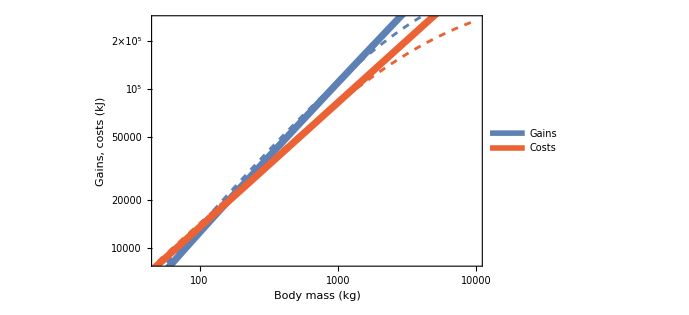

```mathematica
PlotGainCost=Legended[Show[
muExp = -3.1;
LogLogPlot[costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[97,4]],Frame->True,FrameLabel->{"Body mass (kg)","Gains,  costs (kJ)"},LabelStyle->Directive[FontSize->16,Black],FrameStyle->Black(*,PlotLegends->LineLegend[{ColorData[97,1],ColorData[97,4]},{"Gains","Costs"}]*)],
LogLogPlot[gainsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[97,1]],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
ListLogLogPlot[simgain,PlotStyle->Directive[Thickness[0.01],ColorData[97,1]],Joined->True],
ListLogLogPlot[simcost,PlotStyle->Directive[Thickness[0.01],ColorData[97,4]],Joined->True]
,ImageSize->510],
Placed[LineLegend[{Directive[ColorData[97,1],Thickness[0.02]],Directive[ColorData[97,4],Thickness[0.02]]},{"Gains","Costs"},LegendMarkerSize->14,LabelStyle->Directive[FontSize->14]],Scaled[{0.1,0.875}]]
]
```

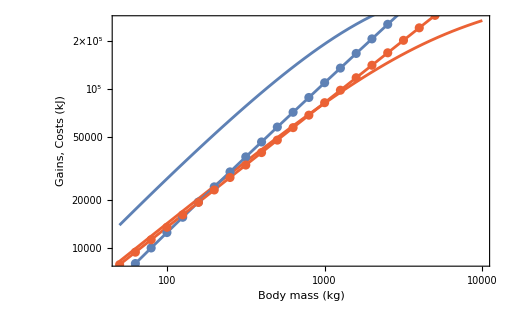

```mathematica
PlotGainCostDelta = Show[
muExp = -3.1;
LogLogPlot[costsParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Thickness[0.004],ColorData[97,4]],Frame->True,FrameLabel->{"Body mass (kg)","Gains,  Costs (kJ)"},LabelStyle->Directive[FontSize->16,Black],FrameStyle->Black],
LogLogPlot[gainsDeltaParam/.{α->4,μ->10^muExp,ζ->zetavec[[1]]},{M,50,10000},PlotStyle->Directive[Thickness[0.004],ColorData[97,1]],Frame->True,FrameLabel->{"Body mass (kg)","Costs (kJ)"}],
ListLogLogPlot[simgain,PlotStyle->ColorData[97,1],Joined->True],
ListLogLogPlot[simcost,PlotStyle->ColorData[97,4],Joined->True],
ListLogLogPlot[simgain,PlotStyle->ColorData[97,1]],
ListLogLogPlot[simcost,PlotStyle->ColorData[97,4]],
Epilog->{Inset[insetPlot,Scaled[{0.98,0.6}],{Right,Top}]}
,ImageSize->510
]
```

```mathematica
gainsValues = Table[{10^i,gainsParam/.{μ->10^-5,α->4,ζ->1,M->10^i}},{i,3,4.5,0.1}];
(*Assume neValues is defined as in your code*)
loggainsValues=Log10@gainsValues;
(*Fit a linear model to the log-log data*)
fit=LinearModelFit[loggainsValues,x,x]
(*Extract the slope*)
slope=fit["BestFitParameters"][[2]]
```

FittedModel[…]

0.933121

```mathematica
gainslope = LogDerivative[gainsParam,M]
```

1/M^0.093 0.00150782 ((724.886 M^0.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))-(663.208 M^1.093 (0.000621411 M^0.165+(0.003356 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) α)/(M^0.161 (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)-(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(2 (-2+ζ)) M^0.839 α^2 (-2+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ)+(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) M^0.839 α (-1+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^2) (0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

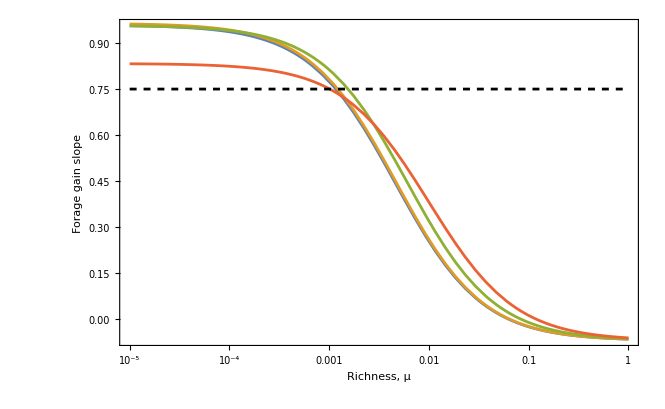

```mathematica
Show[
Flatten[{
Table[
LogLinearPlot[gainslope/.{M->1000,α->4,ζ->zetavec[[i]]},{μ,10^-5,10^0},PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Richness, μ","Forage gain slope"},LabelStyle->Directive[FontSize->16]],
{i,1,Length[zetavec]}],
LogLinearPlot[0.75,{μ,10^-5,10^0},PlotStyle->Directive[Dashed,Black]]},1]
]
```

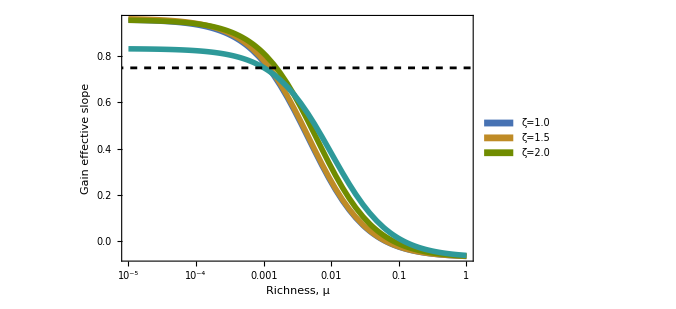

```mathematica
CD = 86;
PlotGainSlopeMu = Show[
Flatten[{
LogLinearPlot[gainslope/.{M->1000,α->4,ζ->zetavec[[1]]},{μ,10^-5,10^0},PlotStyle->Directive[Thickness[0.008],ColorData[CD,1]],Frame->True,FrameLabel->{"Richness, μ","Gain effective slope"},LabelStyle->Directive[FontSize->16,Black],FrameStyle->Black,PlotLegends->Placed[SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3]},{"ζ=1.0","ζ=1.5","ζ=2.0"}],{Scaled[{0.01,0.25}], {0, 0.5}}]],
Table[
LogLinearPlot[gainslope/.{M->1000,α->4,ζ->zetavec[[i]]},{μ,10^-5,10^0},PlotStyle->Directive[Thickness[0.008],ColorData[CD,i]],Frame->True,FrameLabel->{"Richness, μ","Gain effective slope"},LabelStyle->Directive[FontSize->16]]
,{i,2,Length[zetavec]}],
LogLinearPlot[0.75,{μ,10^-6,10^1},PlotStyle->Directive[Dashed,Black]]
},1]
,ImageSize->500
]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainslopemu.pdf"],PlotGainSlopeMu]
```

/Users/jdyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainslopemu.pdf

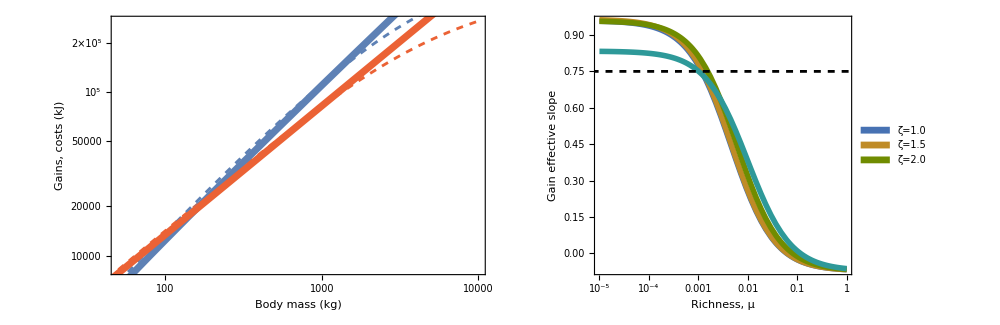

```mathematica
PlotGainRow =GraphicsRow[{PlotGainCost,PlotGainSlopeMu},ImageSize->1000,Spacings->0]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainrow.pdf"],PlotGainRow]
```

/Users/jdyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainrow.pdf

```mathematica
gainscostsratioParam = gainsParam/costsParam;
```

```mathematica
simgaincostzeta10 = Import[StringJoin[namespace,"/herbforagingsim/data/simdata/gaincostpoor_zeta1_data.csv"]][[2;;All]];
simgaincostzeta15 = Import[StringJoin[namespace,"/herbforagingsim/data/simdata/gaincostpoor_zeta15_data.csv"]][[2;;All]];
simgaincostzeta20 = Import[StringJoin[namespace,"/herbforagingsim/data/simdata/gaincostpoor_zeta20_data.csv"]][[2;;All]];
simgaincostzeta215 = Import[StringJoin[namespace,"/herbforagingsim/data/simdata/gaincostpoor_zeta215_data.csv"]][[2;;All]];
```

```mathematica
simgainzeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,2]]}];
simcostzeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,3]]}];
simgainzeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,2]]}];
simcostzeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,3]]}];
simgainzeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,2]]}];
simcostzeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,3]]}];
simgainzeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,2]]}];
simcostzeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,3]]}];
```

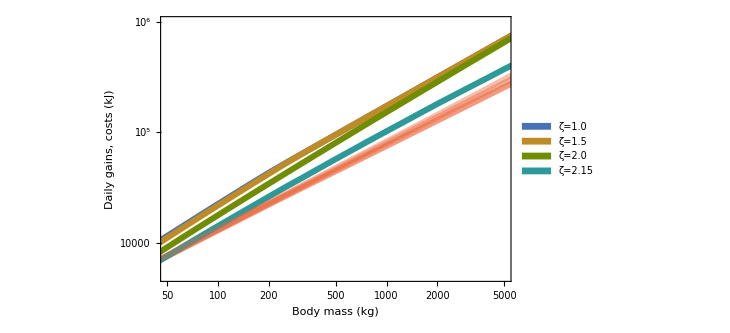

```mathematica
CD = 86;
PlotGainsZeta = Show[
ListLogLogPlot[simgainzeta10,PlotStyle->Directive[Thickness[0.008],ColorData[86,1]],Joined->True,Frame->True,FrameLabel->{"Body mass (kg)","Daily gains, costs (kJ)"},PlotRange->{{50,5000},{5000,1*10^6}},LabelStyle->Directive[Black,FontSize->16],PlotLegends->Placed[SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3],ColorData[CD,4]},{"ζ=1.0","ζ=1.5","ζ=2.0","ζ=2.15"}],{Scaled[{0.01,0.75}], {0, 0.5}}]],
ListLogLogPlot[simcostzeta10,PlotStyle->Directive[Thickness[0.008],Opacity[0.4],ColorData[97,4]],Joined->True],

ListLogLogPlot[simgainzeta15,PlotStyle->Directive[Thickness[0.008],ColorData[86,2]],Joined->True],
ListLogLogPlot[simcostzeta15,PlotStyle->Directive[Thickness[0.008],Opacity[0.4],ColorData[97,4]],Joined->True],

ListLogLogPlot[simgainzeta20,PlotStyle->Directive[Thickness[0.008],ColorData[86,3]],Joined->True],
ListLogLogPlot[simcostzeta20,PlotStyle->Directive[Thickness[0.008],Opacity[0.4],ColorData[97,4]],Joined->True],

ListLogLogPlot[simgainzeta215,PlotStyle->Directive[Thickness[0.008],ColorData[86,4]],Joined->True],
ListLogLogPlot[simcostzeta215,PlotStyle->Directive[Thickness[0.008],Opacity[0.4],ColorData[97,4]],Joined->True], ImageSize->540
]
```

```mathematica
simgaincostratiozeta10 = Transpose[{simgaincostzeta10[[All,1]],simgaincostzeta10[[All,2]]/simgaincostzeta10[[All,3]]}];
simgaincostratiozeta15 = Transpose[{simgaincostzeta15[[All,1]],simgaincostzeta15[[All,2]]/simgaincostzeta15[[All,3]]}];
simgaincostratiozeta20 = Transpose[{simgaincostzeta20[[All,1]],simgaincostzeta20[[All,2]]/simgaincostzeta20[[All,3]]}];
simgaincostratiozeta215 = Transpose[{simgaincostzeta215[[All,1]],simgaincostzeta215[[All,2]]/simgaincostzeta215[[All,3]]}];
```

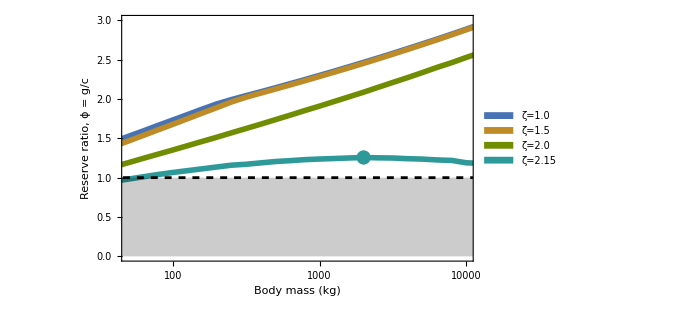

```mathematica
CD = 86;
PlotGainsCostsRatioZeta = Show[
ListLogLinearPlot[simgaincostratiozeta10,PlotStyle->Directive[Thickness[0.008],ColorData[86,1]],Joined->True,Frame->True,FrameLabel->{"Body mass (kg)","Reserve ratio, ϕ = g/c"},PlotRange->{{50,10000},{0,3}},LabelStyle->Directive[Black,FontSize->16],PlotLegends->Placed[SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3],ColorData[CD,4]},{"ζ=1.0","ζ=1.5","ζ=2.0","ζ=2.15"}],{Scaled[{0.01,0.80}], {0, 0.5}}]],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->1},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,4]]],*)

ListLogLinearPlot[simgaincostratiozeta15,PlotStyle->Directive[Thickness[0.008],ColorData[86,2]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->1.5},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,2]]],*)

ListLogLinearPlot[simgaincostratiozeta20,PlotStyle->Directive[Thickness[0.008],ColorData[86,3]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->2},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,3]]],*)

ListLogLinearPlot[simgaincostratiozeta215,PlotStyle->Directive[Thickness[0.008],ColorData[86,4]],Joined->True],
(*LogLinearPlot[gainscostsratioParam/.{μ->10^-2.8,α->4,ζ->2.15},{M,50,10^4},PlotStyle->Directive[Dashed,ColorData[CD,4]]],*)

LogLinearPlot[1,{M,10,50000},PlotStyle->Directive[Dashed,Black],Filling->Bottom],
ListLogLinearPlot[{simgaincostratiozeta215[[Position[simgaincostratiozeta215[[All,2]],Max[simgaincostratiozeta215[[All,2]]]][[1]][[1]]]]},PlotStyle->Directive[PointSize[0.02],ColorData[86,4]]], ImageSize->500
]
```

```mathematica
Position[simgaincostratiozeta215[[All,2]],Max[simgaincostratiozeta215[[All,2]]]][[1]][[1]]
```

19

```mathematica
simgaincostratiozeta215[[Position[simgaincostratiozeta215[[All,2]],Max[simgaincostratiozeta215[[All,2]]]][[1]][[1]]]]
```

{1995.26,1.25624}

```mathematica
simgaincostratiozeta215
```

{{31.6228,0.922855},{39.8107,0.953292},{50.1187,0.982197},{63.0957,1.01099},{79.4328,1.0395},{100.,1.06539},{125.893,1.08861},{158.489,1.11191},{199.526,1.13507},{251.189,1.15812},{316.228,1.17005},{398.107,1.1876},{501.187,1.20463},{630.957,1.21589},{794.328,1.22849},{1000.,1.23655},{1258.93,1.24266},{1584.89,1.24978},{1995.26,1.25624},{2511.89,1.25146},{3162.28,1.24913},{3981.07,1.24077},{5011.87,1.23548},{6309.57,1.22482},{7943.28,1.21867},{10000.,1.18832},{12589.3,1.18174},{15848.9,1.14176},{19952.6,1.12464},{25118.9,1.08055}}

```mathematica
{1995.2623149688789,1.2562394629583369}
```

```mathematica
Max[simgaincostratiozeta215[[All,2]]]
```

1.25624

```mathematica
Position[simgaincostratiozeta215[[All,2]],Max[simgaincostratiozeta215[[All,2]]]][[1]][[1]]
```

19

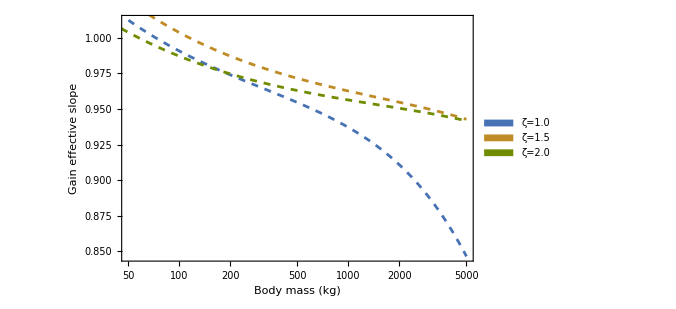

```mathematica
CD = 86;
PlotGainSlopeMass = Show[
Flatten[{
LogLinearPlot[gainslope/.{μ->10^-4,α->4,ζ->zetavec[[1]]},{M,50,5000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[CD,1]],Frame->True,FrameLabel->{"Body mass (kg)","Gain effective slope"},LabelStyle->Directive[FontSize->16],PlotLegends->Placed[SwatchLegend[{ColorData[CD,1],ColorData[CD,2],ColorData[CD,3]},{"ζ=1.0","ζ=1.5","ζ=2.0"}],{Scaled[{0.01,0.25}], {0, 0.5}}]],
Table[
LogLinearPlot[gainslope/.{μ->10^-5,α->4,ζ->zetavec[[i]]},{M,10,5000},PlotStyle->Directive[Dashed,Thickness[0.004],ColorData[CD,i]],Frame->True,FrameLabel->{"Body mass (kg)","Travel time (s/bite)"},LabelStyle->Directive[FontSize->16]]
,{i,2,Length[zetavec]}],
LogLinearPlot[0.75,{M,10,10000},PlotStyle->Directive[Dashed,Black]]
},1]
,ImageSize->500
]
```

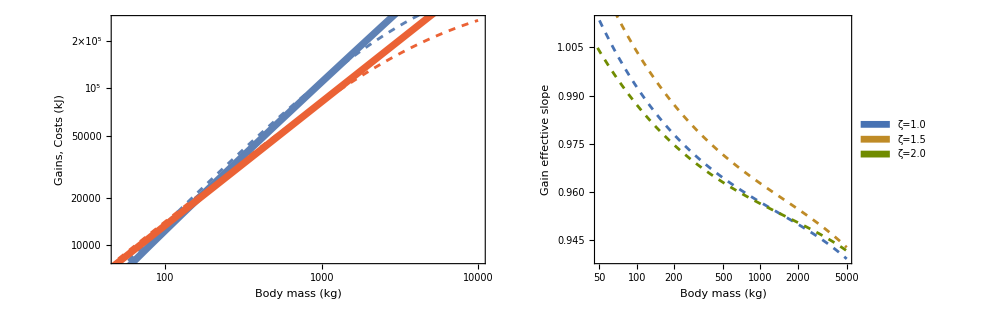

```mathematica
PlotGainRowV2 =GraphicsRow[{PlotGainCost,PlotGainSlopeMass},ImageSize->1000,Spacings->0]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainrowv2.pdf"],PlotGainRowV2]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainrowv2.pdf

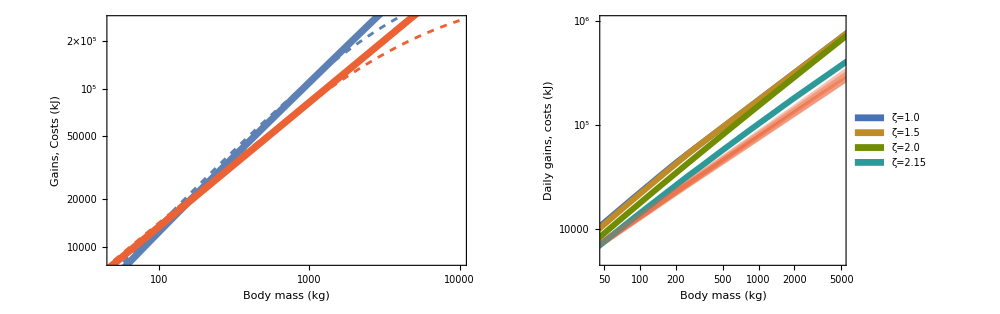

```mathematica
PlotGainRowV3 =GraphicsRow[{PlotGainCost,PlotGainsZeta},ImageSize->1000,Spacings->1]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainrowv3.pdf"],PlotGainRowV3]
```

/Users/jdyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainrowv3.pdf

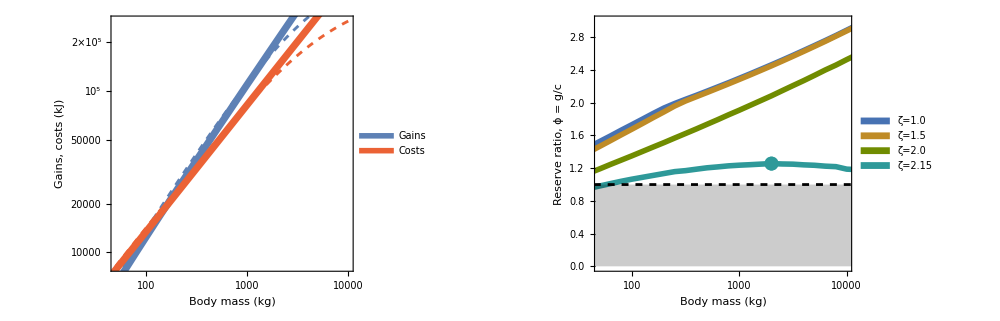

```mathematica
PlotGainRowV4 =GraphicsRow[{PlotGainCost,PlotGainsCostsRatioZeta},ImageSize->1000,Spacings->1]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainrowv4.pdf"],PlotGainRowV4]
```

/Users/justinyeakel/Dropbox/PostDoc/2025_fatscaling/figures/fig_gainrowv4.pdf

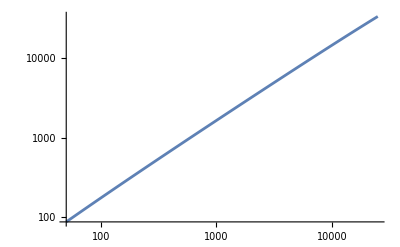

```mathematica
LogLogPlot[gainsParam/.{μ->10^-5,α->4,ζ->zetavec[[1]]},{M,50,25000}]
```

```mathematica
Export[StringJoin[namespace,"/figures/fig_gainslopemass.pdf"],PlotGainSlopeMass]
```

/Users/justinyeakel/Dropbox/PostDoc/2024_herbforaging/figures/fig_gainslopemass.pdf

```mathematica
gainremainderParam = gainsParam - c0*M^c1/.{c0->Exp[5.86],c1->0.79} (*Updated values 4/15/2025*)
```

-350.724 M^0.79+(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))

```mathematica
gainremainderslope = LogDerivative[gainremainderParam,M]
```

(M (-277.072/M^0.21+(724.886 M^0.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))-(663.208 M^1.093 (0.000621411 M^0.165+(0.003356 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) α)/(M^0.161 (-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)-(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(2 (-2+ζ)) M^0.839 α^2 (-2+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α)^2 μ)+(0.004 (-0.802022/M^2.21233-0.459916/M^1.69033) ((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) M^0.839 α (-1+ζ))/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ))^2))/(-350.724 M^0.79+(663.208 M^1.093)/(0.0005334 M^1.165+(0.004 ((0.661552+0.666223 M^0.522)/M^1.21233)^(-1+ζ) M^0.839 α)/((-1+((0.661552+0.666223 M^0.522)/M^1.21233)^(-2+ζ) α) μ)))

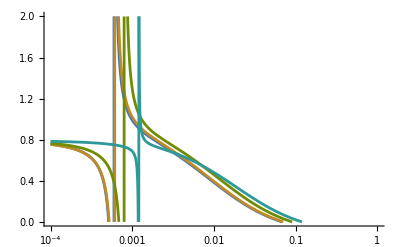

```mathematica
Show[
Table[
LogLinearPlot[gainremainderslope/.{M->500,α->4,ζ->zetavec[[i]]},{μ,10^-4,10^0},PlotRange->{0,2},PlotStyle->ColorData[86,i]],
{i,1,Length[zetavec]}]
(*,
LogLinearPlot[0.788,{μ,10^-5,10^0},PlotStyle->Directive[Dashed,Black]]*)
]
```

```mathematica
gainremainderslopeValues = Table[{10^i,gainremainderslope/.{M->500,α->4,μ->10^i,ζ->1}},{i,-3.5,0,0.01}];
```

```mathematica
Export[StringJoin[namespace,"/herbforagingsim/data/expgainremainderslope.CSV"],gainremainderslopeValues]
```

/Users/jdyeakel/Dropbox/PostDoc/2024_herbforaging/herbforagingsim/data/expgainremainderslope.CSV

```mathematica
expD = (α*np^(ζ-1))/(m*(α*np^(ζ-2)-1))
```

(np^(-1+ζ) α)/(m (-1+np^(-2+ζ) α))

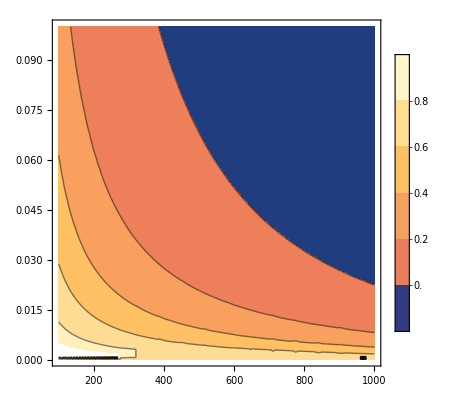

```mathematica
ContourPlot[gainremainderslope/.{α->4,ζ->1},{M,100,1000},{μ,10^-4,10^-1},PlotLegends->Automatic]
```

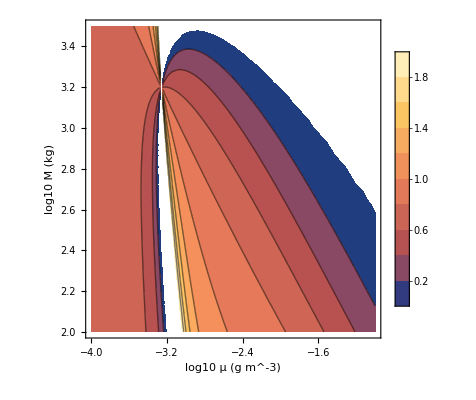

```mathematica
(*rename the log variables for clarity*)With[{expr=gainremainderslope/. {α->4,ζ->1}},ContourPlot[Evaluate[expr/. {M->10^m,μ->10^n}],(*10^2–10^3->100–1000 kg*){n,-4,-1},(*10^m=M,10^n=μ*){m,2,3.5},(*10^-4–10^-1 g m^-3*)FrameLabel->{"log10 μ (g m^-3)","log10 M (kg)"},PlotRange->{0,2},PlotLegends->Automatic,Ticks->{Table[{i,10^i},{i,2,3}],(*show ticks as original values*)Table[{j,10^j},{j,-4,-1}]}]]
```

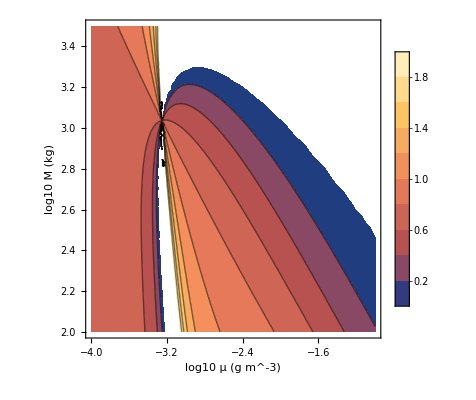

```mathematica
(*rename the log variables for clarity*)With[{expr=(Log[gainremainderParam/.M->10^(m*1.1)]-Log[gainremainderParam/.M->10^(m)])/(Log[10^(m*1.1)]-Log[10^(m)])/. {α->4,ζ->1}},ContourPlot[Evaluate[expr/. {μ->10^n}],(*10^2–10^3->100–1000 kg*){n,-4,-1},(*10^m=M,10^n=μ*){m,2,3.5},(*10^-4–10^-1 g m^-3*)FrameLabel->{"log10 μ (g m^-3)","log10 M (kg)"},PlotRange->{0,2},PlotLegends->Automatic,Ticks->{Table[{i,10^i},{i,2,3}],(*show ticks as original values*)Table[{j,10^j},{j,-4,-1}]}]]
```

The Effective slope for the GENERAL relationship:

```mathematica
γ[c1_,g1_] := 1-(c1-g1)/(1.19-g1)
```

```mathematica
γ[0.76,0.86]
```

1.30303

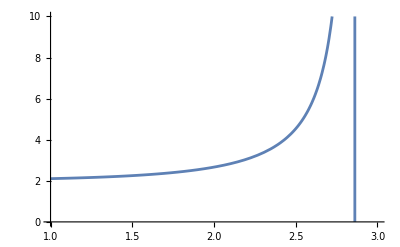

```mathematica
Plot[expD/.{α->4,np->0.2,m->0.1},{ζ,1,3},PlotRange->{0,10}]
```

```mathematica
xMin=100(*lower end of large M range*);
xMax=10000(*upper end of large M range*);
averageSlope=(Log[gainremainderParam/.M->xMax]-Log[gainremainderParam/.M->xMin])/(Log[xMax]-Log[xMin])/.{α->4,ζ->1}
```

(-Log[-13334.2+101777./(0.114039+0.00580264/μ)]+Log[-506951.+(1.56189×10^7)/(24.3811+0.0105677/μ)])/(-Log[100]+Log[10000])

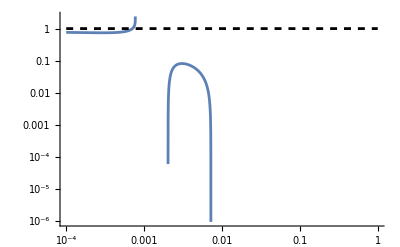

```mathematica
Show[
LogLogPlot[averageSlope,{μ,10^-4,10^0},PlotRange->All],
LogLogPlot[1,{μ,10^-4,10^0},PlotStyle->Directive[Black,Dashed]]
]
```

```mathematica
NSolve[averageSlope==1.19,μ]
```

{{μ→-0.000377126},{μ→0.000746885}}

```mathematica
(*muObservedSlope = Table[
gainremainderslopeSpecific = gainremainderslope/.{α->4,ζ->1,M->10^i};
{10^i,Max[μ/. NSolve[gainremainderslopeSpecific==1.19,μ]]},{i,2,5,0.01}];*)
muObservedSlope = Table[
xMin=10^i(*lower end of large M range*);
xMax=10^(i*1.1)(*upper end of large M range*);
averageSlope=(Log[gainremainderParam/.M->xMax]-Log[gainremainderParam/.M->xMin])/(Log[xMax]-Log[xMin])/.{α->4,ζ->1};
muslope = Max[μ/. NSolve[averageSlope==1.19,μ]];
SweptVolume = nefullParam*ExpVolumeParam;
{10^i,ϵ*muslope(**SweptVolume*)(*gainremainderParam/(ϵ*muslope*SweptVolume)*)(*(muslope*ϵ)/gainremainderParam*)/.{M->10^i,α->4,ζ->1,μ->muslope,ϵ->18.2}},{i,2,4,0.01}];
```

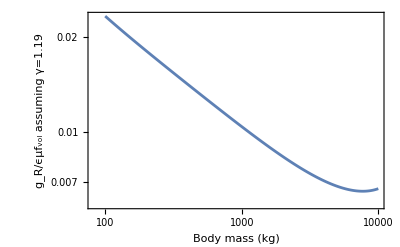

```mathematica
ListLogLogPlot[muObservedSlope,Frame->True,FrameLabel->{"Body mass (kg)","g_R/ϵμf_vol assuming γ=1.19"},(*PlotRange->{10^-3,10^0},*)Joined->True]
```

```mathematica
distanceratio = Table[
xMin=10^i(*lower end of large M range*);
xMax=10^(i*1.1)(*upper end of large M range*);
averageSlope=(Log[gainremainderParam/.M->xMax]-Log[gainremainderParam/.M->xMin])/(Log[xMax]-Log[xMin])/.{α->4,ζ->1};
muslope = Max[μ/. NSolve[averageSlope==1.19,μ]];
{10^i,(ExpDParam/.μ->muslope)/(ExpDParam/.μ->10^-2)(*(ExpDParam/.μ->muslope)/(ExpDParam/.μ->10^-1)*)/.{M->10^i,α->4,ζ->1,ϵ->18.2}},{i,2,4.5,0.01}];
```

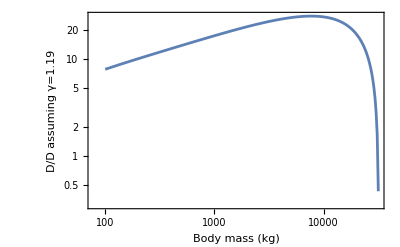

```mathematica
ListLogLogPlot[distanceratio,Frame->True,FrameLabel->{"Body mass (kg)","D/D assuming γ=1.19"},(*PlotRange->{10^-3,10^0},*)Joined->True]
```

```mathematica
(*Assume neValues is defined as in your code*)
logValues=Log10@distanceratio[[1;;50]];
(*Fit a linear model to the log-log data*)
fit=LinearModelFit[logValues,x,x]
(*Extract the slope*)
slope=fit["BestFitParameters"][[2]]
```

FittedModel[…]

0.356534